```mathematica
SetDirectory[NotebookDirectory[]];
```

## Examine RoA

```mathematica
RoAList=Import["RoAListQuarters02-05.dat"];
```

```mathematica
R0AArray=Table[RoAList[[i,3]],{i,1,Length[RoAList]}];
```

```mathematica
RoAListBest={};
Do[If[RoAList[[i,3]]>1.8,RoAListBest=Append[RoAListBest,{RoAList[[i,1]],RoAList[[i,2]],RoAList[[i,3]]}]],{i,1,Length[RoAList]}]
RoAListBest
```

{{8300,0.056,2.01574},{8500,0.056,1.80207},{380,0.022,2.15312},{400,0.022,2.1703},{420,0.022,2.2587}}

```mathematica
RoAInt=Interpolation[RoAList]
```

InterpolatingFunction[{{20.,9900.},{0.002,0.08}},<>]

```mathematica
Plot3D[RoAInt[x,y],{x,20,9900},{y,0.002,0.08},PlotRange->{All,All,{-1,5}},ImageSize->1000,AxesLabel->{Style["ChLength",FontSize->20,Italic,Bold],Style["StpPct",FontSize->20,Italic,Bold],Style["RoA",FontSize->20,Italic,Bold]},LabelStyle->{Directive[Black,20],FontFamily->"Calibri"}]
```

-Graphics3D-

## Set the constants and formulas

```mathematica
Slpg=24;
PV=50;
Day=45;
Month=23Day;
```

```mathematica
PL[POut_,PIn_]:=(POut-PIn)PV-Slpg;
```

## Import the data and select the interval of interest

### Load the raw SY data

```mathematica
SetDirectory[NotebookDirectory[]];
Data=Import["SY-5min.asc","FieldSeparators"->","];
```

### Select the start tick used in precomputing the HH and LL lists

```mathematica
nStartDay=100037;
Data[[nStartDay]]
```

{01/08/91,09:35,440.5,442.,440.,441.75,0}

### Set the maximal and minimal channel length and steps in which we jump

```mathematica
ChLengthMax=10000;
ChLengthMin=500;
ChJump=100;
NKids=Quotient[ChLengthMax-ChLengthMin,ChJump];
```

### Put the channel lengths in an array

```mathematica
ChLengthList=Table[ChLengthMax-(i-1)ChJump,{i,1,NKids+1}];
```

### Load relevant OHLC data corresponding to the data in the external HHs and LLs

```mathematica
TradeStart=nStartDay;
TradeStop=TradeStart+48Month+ChLengthMax-1;
DataOHLC=Table[{Data[[i,3]],Data[[i,4]],Data[[i,5]],Data[[i,6]]},{i,TradeStart,TradeStop+ChLengthMax,1}];
Length[DataOHLC]
```

69680

### Load the external HH and LL lists for four years

```mathematica
HHExt1=Import["HH95KidsYear1.dat"];
HHExt2=Import["HH95KidsYear2.dat"];
HHExt3=Import["HH95KidsYear3.dat"];
HHExt4=Import["HH95KidsYear4.dat"];
LLExt1=Import["LL95KidsYear1.dat"];
LLExt2=Import["LL95KidsYear2.dat"];
LLExt3=Import["LL95KidsYear3.dat"];
LLExt4=Import["LL95KidsYear4.dat"];
```

### Set all the arrays to the same starting point

```mathematica
OpenList=Table[DataOHLC[[i,1]],{i,ChLengthMax+1,ChLengthMax+48Month}];
HighList=Table[DataOHLC[[i,2]],{i,ChLengthMax+1,ChLengthMax+48Month}];
LowList=Table[DataOHLC[[i,3]],{i,ChLengthMax+1,ChLengthMax+48Month}];
CloseList=Table[DataOHLC[[i,4]],{i,ChLengthMax+1,ChLengthMax+48Month}];
```

## The main code with optimal parameters

```mathematica
ChLengthOpt=7500;
StpPctOpt=0.035;
```

```mathematica
ChNum=Position[ChLengthList,ChLengthOpt][[1,1]];
HHList=Join[Table[HHExt1[[i,ChNum]],{i,1,Length[HHExt1]}],Table[HHExt2[[i,ChNum]],{i,1,Length[HHExt2]}],Table[HHExt3[[i,ChNum]],{i,1,Length[HHExt3]}],Table[HHExt4[[i,ChNum]],{i,1,Length[HHExt4]}]];
LLList=Join[Table[LLExt1[[i,ChNum]],{i,1,Length[LLExt1]}],Table[LLExt2[[i,ChNum]],{i,1,Length[LLExt2]}],Table[LLExt3[[i,ChNum]],{i,1,Length[LLExt3]}],Table[LLExt4[[i,ChNum]],{i,1,Length[LLExt4]}]];
MPTemp=0;MP=0;Equity=0;TargetPrice=0;EntryPrice=0;PrevPeak=0;PrevTrough=0;DD=0;EquityMax=0;MaxDD=0;EquityList={};MPList={};
Do[
EquityList=Append[EquityList,{i,Equity}];
MPList=Append[MPList,{i,MP}];
If[Equity>EquityMax,EquityMax=Equity;];
DD=Equity-EquityMax;
If[DD<MaxDD,MaxDD=DD;];
If[MP==0,{
If[HighList[[i]]>HHList[[i]]&&OpenList[[i]]<HHList[[i]],{MPTemp=+1;EntryPrice=HHList[[i]];}];
If[HighList[[i]]>HHList[[i]]&&OpenList[[i]]≥HHList[[i]],{MPTemp=+1;EntryPrice=OpenList[[i]];}];
If[LowList[[i]]<LLList[[i]]&&OpenList[[i]]>LLList[[i]],{MPTemp=-1;EntryPrice=LLList[[i]];}];
If[LowList[[i]]<LLList[[i]]&&OpenList[[i]]≤LLList[[i]],{MPTemp=-1;EntryPrice=OpenList[[i]];}];
}];
If[MP==+1,{
PrevPeak=EntryPrice;
If[CloseList[[i-1]]>PrevPeak,PrevPeak=CloseList[[i-1]];];
TargetPriceRaw=PrevPeak(1-StpPctOpt);
TargetPrice=(Quotient[TargetPriceRaw,0.25]+Quotient[Mod[TargetPriceRaw,0.25],0.125])*0.25;
If[TargetPrice≥LowList[[i]]&&TargetPrice≤OpenList[[i]],{Equity=Equity+PL[TargetPrice,EntryPrice];MPTemp=0;}];
If[TargetPrice≥LowList[[i]]&&TargetPrice>OpenList[[i]],{Equity=Equity+PL[OpenList[[i]],EntryPrice];MPTemp=0;}];
}];
If[MP==-1,{
PrevTrough=EntryPrice;
If[CloseList[[i-1]]<PrevTrough,PrevTrough=CloseList[[i-1]];];
TargetPriceRaw=PrevTrough(1+StpPctOpt);
TargetPrice=(Quotient[TargetPriceRaw,0.25]+Quotient[Mod[TargetPriceRaw,0.25],0.125])*0.25;
If[TargetPrice≤HighList[[i]]&&TargetPrice≥OpenList[[i]],{Equity=Equity+PL[EntryPrice,TargetPrice];MPTemp=0;}];
If[TargetPrice≤HighList[[i]]&&TargetPrice<OpenList[[i]],{Equity=Equity+PL[EntryPrice,OpenList[[i]]];MPTemp=0;}];
}];
MP=MPTemp;
,{i,1,Length[HHList],1}];
If[MP==+1,Equity=Equity+PL[CloseList[[48Month]],EntryPrice];];
If[MP==-1,Equity=Equity+PL[EntryPrice,CloseList[[48Month]]];];
If[Equity>EquityMax,EquityMax=Equity;];
EquityList=Append[EquityList,{i,Equity}];
```

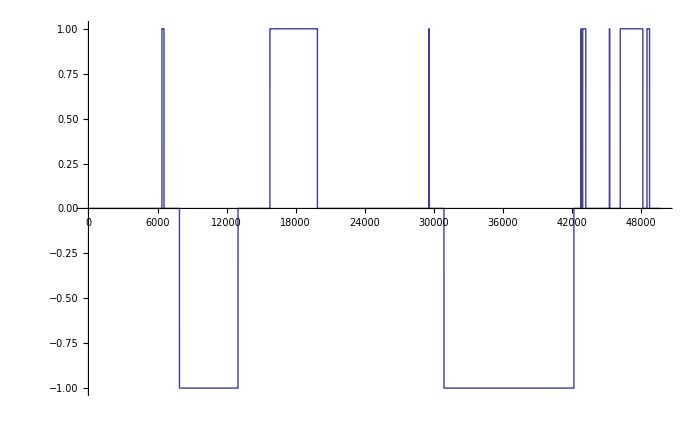

```mathematica
ListPlot[MPList,Joined->True,ImageSize->700]
```

```mathematica
Export["MPListStable.dat",MPList]
```

MPListStable.dat

```mathematica
Export["EquityListStable.dat",EquityList]
```

EquityListStable.dat

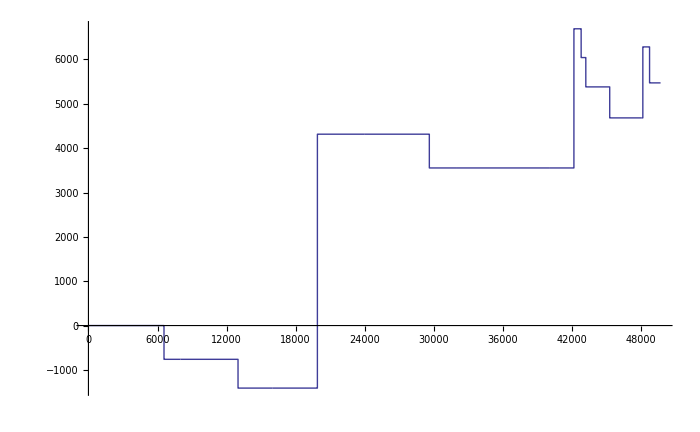

```mathematica
plpl=ListPlot[EquityList,Joined->True,ImageSize->700]
```

```mathematica
Closes=Table[{i,CloseList[[i]]},{i,1,Length[CloseList]}];
```

```mathematica
Export["CloseList.dat",Closes]
```

CloseList.dat

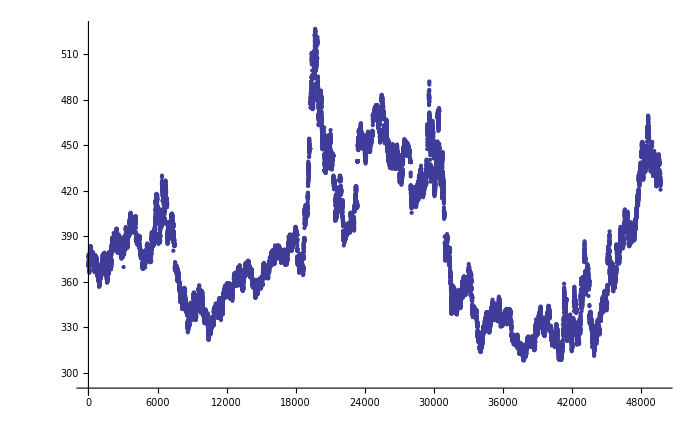

```mathematica
ListPlot[Closes,ImageSize->700]
```